## Color Palette

```mathematica
originalColorsValues={
{70,100,0,0},
{40,60,0,0},
{50,100,0,0},
{100,100,100,100},
{0,0,0,0}
};
colorPalette=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues
```

{CMYKColor[Rational[7, 10], 1, 0, 0],CMYKColor[Rational[2, 5], Rational[3, 5], 0, 0],CMYKColor[Rational[1, 2], 1, 0, 0],CMYKColor[1, 1, 1, 1],CMYKColor[0, 0, 0, 0]}

## City

```mathematica
countryName={"Florence", "Toscana", "Italy"};
(**)
SetDirectory[NotebookDirectory[]];
latLongs=Reverse[CityData[countryName,"Coordinates"]];
polygon=CityData[countryName,"Polygon"];
```

```mathematica
latLongs
```

{11.24,43.78}

```mathematica
CityData[{"Florence", "Toscana", "Italy"}]
```

Florence

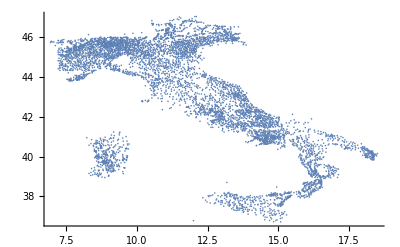

```mathematica
ListPlot[latLongs]
```

```mathematica
sizes=Rescale[#,{Log[populations]//Min,Log[populations]//Max},{.05,2}]&/@Log[populations];
gridSize=14.75;
center={39.50,-26.00};
(**)
GeoGraphics[{
Quiet[GeoPosition/@CityData[{All,countryName}]],
GeoStyling[EdgeForm[Directive[Opacity[1],Thickness[.040],Darker[colorPalette[[5]],.06]]],Opacity[.9],colorPalette[[1]]],
CountryData[countryName,"SchematicPolygon"],
GeoStyling[EdgeForm[Directive[Opacity[1],Thickness[.0075],colorPalette[[5]]]],Opacity[.2],colorPalette[[3]]],
CountryData[countryName,"SchematicPolygon"],
GeoStyling[EdgeForm[Directive[Opacity[.25],Thickness[.020],colorPalette[[2]]]],Opacity[0],colorPalette[[5]]],
CountryData[countryName,"Polygon"]
}
,AspectRatio->1
,Axes->False
,Background->Directive[{colorPalette[[5]],Opacity[1]}]
,Frame->True
,FrameStyle->Directive[colorPalette[[4]],Thickness[.0035]]
,FrameTicks->None
,FrameTicksStyle->White
,GridLines->Automatic
,GridLinesStyle->Directive[{Dashed,Thickness[.001],colorPalette[[4]]}]
,ImageSize->750
(*,PlotRange->({#,#+gridSize}&/@center)*)
,GeoBackground->None
,Prolog->{colorPalette[[1]],Opacity[.00005],EdgeForm[Directive[Opacity[.00000005],Thickness[.0025],colorPalette[[1]]]],polygon}
,Epilog->{
White,
Opacity[.9],
EdgeForm[Directive[Thickness[.004],Opacity[1],Black]],
DeleteCases[Disk[#[[1]],#[[2]]/10]&/@Transpose[{latLongs,sizes//N}],Disk[Missing["NotAvailable"],_]],
Black,
Opacity[1],
Text[
Style[countryName,75,Lighter[colorPalette[[4]],.25],FontFamily->"Zapfino"
],{center[[1]]+.775gridSize,center[[2]]+gridSize*.09}]
}
]
(*Export["ModernMadagascar.png",%,ImageSize->7500]
Export["Madagascar_Coordinates.csv",latLongs]
(**)
populations=Normal[CityData[#,"Population"]&/@CityData[{All,countryName}]];
Export["Madagascar_Populations.csv",populations]*)
```

$Aborted

## Country

```mathematica
countryName="Italy";
popsNumber=30;
SetDirectory[NotebookDirectory[]];
(**)
populations=Normal[CityData[#,"Population"]&/@CityData[{All,countryName}]];
selectedPopSizes=(Reverse[populations//Sort])[[1;;popsNumber]];
indices=Flatten[Position[populations,#]&/@selectedPopSizes];
(**)
latLongs=Reverse[CityData[#,"Coordinates"]]&/@CityData[{All,countryName}][[indices]];
populations=populations[[indices]];
```

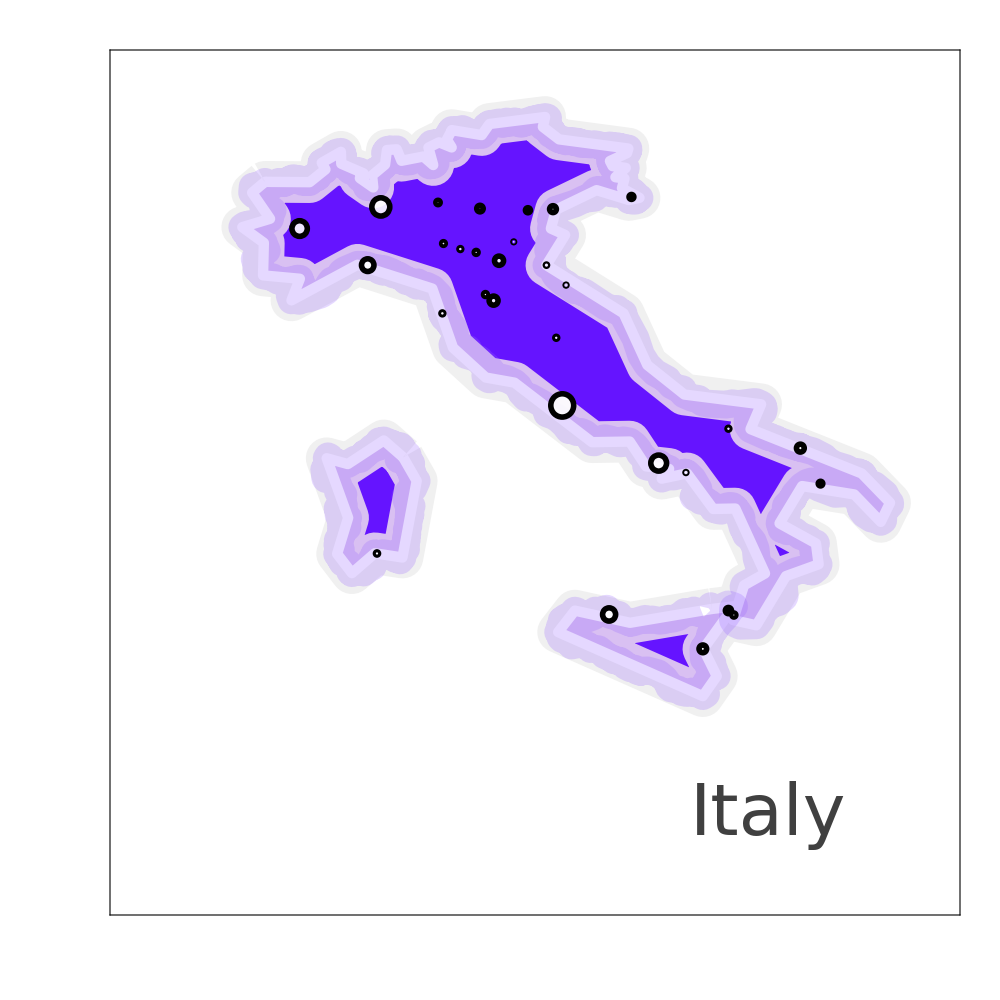

Italy.png

Italy_Coordinates.csv

Italy_Populations.csv

```mathematica
sizes=Rescale[#,{Log[populations]//Min,Log[populations]//Max},{.05,2}]&/@Log[populations];
gridSize=15;(*14.75;*)
center={4.5,33};(*{39.50,-26.00};*)
(**)
GeoGraphics[{
(*Quiet[GeoPosition/@CityData[{All,countryName}]],*)
GeoStyling[EdgeForm[Directive[Opacity[1],Thickness[.030],Darker[colorPalette[[5]],.06]]],Opacity[.9],colorPalette[[1]]],
CountryData[countryName,"SchematicPolygon"],
GeoStyling[EdgeForm[Directive[Opacity[1],Thickness[.0075],colorPalette[[5]]]],Opacity[.2],colorPalette[[3]]],
CountryData[countryName,"SchematicPolygon"],
GeoStyling[EdgeForm[Directive[Opacity[.25],Thickness[.020],colorPalette[[2]]]],Opacity[0],colorPalette[[5]]],
CountryData[countryName,"Polygon"]
}
,AspectRatio->1
,Axes->False
,Background->Directive[{colorPalette[[5]],Opacity[1]}]
,Frame->True
,FrameStyle->Directive[colorPalette[[4]],Thickness[.0035]]
,FrameTicks->None
,FrameTicksStyle->White
,GridLines->Automatic
,GridLinesStyle->Directive[{Dashed,Thickness[.001],colorPalette[[4]]}]
,ImageSize->1000
,PlotRange->({#,#+gridSize}&/@center)
,GeoBackground->None
,Prolog->{colorPalette[[1]],Opacity[.00005],EdgeForm[Directive[Opacity[.00000005],Thickness[.0025],colorPalette[[1]]]]}
,Epilog->{
White,
Opacity[.9],
EdgeForm[Directive[Thickness[.004],Opacity[1],Black]],
DeleteCases[Disk[#[[1]],.01+#[[2]]/10]&/@Transpose[{latLongs,sizes//N}],Disk[Missing["NotAvailable"],_]],
Black,
Opacity[1],
Text[
Style[countryName,75,Lighter[colorPalette[[4]],.25],FontFamily->"Zapfino"
],{center[[1]]+.785gridSize,center[[2]]+gridSize*.1}]
}
]
Export[countryName<>".png",%,ImageSize->7500]
Export[countryName<>"_Coordinates.csv",latLongs]
Export[countryName<>"_Populations.csv",populations]
```

## Bioko

```mathematica
({#,#+gridSize}&/@(center-center/2))
```

{{5.385,20.385},{0.935,15.935}}

```mathematica
countryName="Equatorial Guinea";
popsNumber=8;
SetDirectory[NotebookDirectory[]];
(**)
populations=Normal[CityData[#,"Population"]&/@CityData[{All,countryName}]];
selectedPopSizes=(Reverse[populations//Sort])[[1;;popsNumber]];
indices=Flatten[Position[populations,#]&/@selectedPopSizes];
(**)
latLongs=Reverse[CityData[#,"Coordinates"]]&/@CityData[{All,countryName}][[indices]];
populations=populations[[indices]];
Median/@Transpose[latLongs]
```

{10.67,1.86}

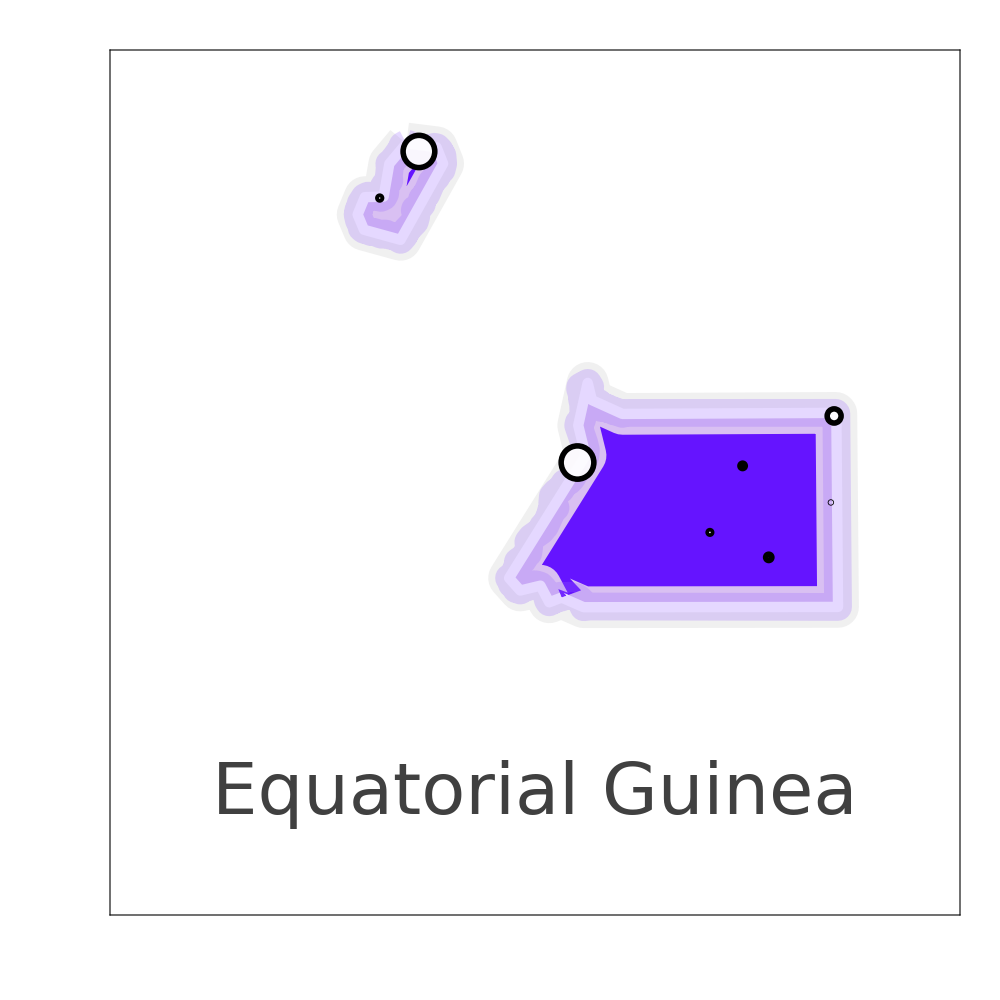

Equatorial Guinea.png

Equatorial Guinea_Coordinates.csv

Equatorial Guinea_Populations.csv

```mathematica
sizes=Rescale[#,{Log[populations]//Min,Log[populations]//Max},{.05,2}]&/@Log[populations];
gridSize=5;(*14.75;*)
center={7,-.75};(*{39.50,-26.00};*)
(**)
GeoGraphics[{
(*Quiet[GeoPosition/@CityData[{All,countryName}]],*)
GeoStyling[EdgeForm[Directive[Opacity[1],Thickness[.030],Darker[colorPalette[[5]],.06]]],Opacity[.9],colorPalette[[1]]],
CountryData[countryName,"SchematicPolygon"],
GeoStyling[EdgeForm[Directive[Opacity[1],Thickness[.0075],colorPalette[[5]]]],Opacity[.2],colorPalette[[3]]],
CountryData[countryName,"SchematicPolygon"],
GeoStyling[EdgeForm[Directive[Opacity[.25],Thickness[.020],colorPalette[[2]]]],Opacity[0],colorPalette[[5]]],
CountryData[countryName,"Polygon"]
}
,AspectRatio->1
,Axes->False
,Background->Directive[{colorPalette[[5]],Opacity[1]}]
,Frame->True
,FrameStyle->Directive[colorPalette[[4]],Thickness[.0035]]
,FrameTicks->None
,FrameTicksStyle->White
,GridLines->Automatic
,GridLinesStyle->Directive[{Dashed,Thickness[.001],colorPalette[[4]]}]
,ImageSize->1000
,PlotRange->({#,#+gridSize}&/@(center))
,GeoBackground->None
,Prolog->{colorPalette[[1]],Opacity[.00005],EdgeForm[Directive[Opacity[.00000005],Thickness[.0025],colorPalette[[1]]]]}
,Epilog->{
White,
Opacity[.9],
EdgeForm[Directive[Thickness[.004],Opacity[1],Black]],
DeleteCases[Disk[#[[1]],.5#[[2]]/10]&/@Transpose[{latLongs,sizes//N}],Disk[Missing["NotAvailable"],_]],
Black,
Opacity[1],
Text[
Style[countryName,75,Lighter[colorPalette[[4]],.25],FontFamily->"Zapfino"
],{center[[1]]+.5gridSize,center[[2]]+gridSize*.125}]
}
]
Export[countryName<>".png",%,ImageSize->7500]
Export[countryName<>"_Coordinates.csv",latLongs]
Export[countryName<>"_Populations.csv",populations]
```

## Fonts

```mathematica
$FontFamilies;
Style[#,25,FontFamily->#]&/@%
```

{Al Bayan,Alegreya SC,Al Nile,Al Tarikh,American Typewriter,Andale Mono,Apple Braille,Apple Chancery,Apple Color Emoji,AppleGothic,AppleMyungjo,Apple SD Gothic Neo,Apple Symbols,Arial,Arial Black,Arial Hebrew,Arial Hebrew Scholar,Arial Narrow,Arial Rounded MT Bold,Arial Unicode MS,Athelas,Avenir,Avenir Next,Avenir Next Condensed,Ayuthaya,Baghdad,Bangla MN,Bangla Sangam MN,Baskerville,Beirut,Big Caslon,Bitstream Vera Sans Mono,Bodoni 72,Bodoni 72 Oldstyle,Bodoni 72 Smallcaps,Bodoni Ornaments,Bradley Hand,Brush Script MT,Chalkboard,Chalkboard SE,Chalkduster,Charter,Clear Sans,Clear Sans Light,Clear Sans Medium,Clear Sans Thin,Cochin,Comic Sans MS,Copperplate,Corsiva Hebrew,Courier,Courier New,Cousine,Damascus,DecoType Naskh,Devanagari MT,Devanagari Sangam MN,Didot,DIN Alternate,DIN Condensed,Diwan Kufi,Diwan Thuluth,Droid Serif,EB Garamond,EB Garamond 12 All SC,EB Garamond SC,Economica,Euphemia UCAS,Farah,Farisi,Felipa,Futura,GB18030 Bitmap,Geeza Pro,Geneva,Gentium Basic,Georgia,Gill Sans,Gujarati MT,Gujarati Sangam MN,Gurmukhi MN,Gurmukhi MT,Gurmukhi Sangam MN,Heiti SC,Heiti TC,Helvetica,Helvetica Neue,Herculanum,Hiragino Kaku Gothic Pro,Hiragino Kaku Gothic ProN,Hiragino Kaku Gothic Std,Hiragino Kaku Gothic StdN,Hiragino Maru Gothic Pro,Hiragino Maru Gothic ProN,Hiragino Mincho Pro,Hiragino Mincho ProN,Hiragino Sans,Hiragino Sans GB,Hoefler Text,Impact,InaiMathi,Inconsolata,Iowan Old Style,ITF Devanagari,ITF Devanagari Marathi,Kailasa,Kalam,Kannada MN,Kannada Sangam MN,Kefa,Khmer MN,Khmer Sangam MN,Kohinoor Bangla,Kohinoor Devanagari,Kohinoor Telugu,Kokonor,Krungthep,KufiStandardGK,Lao MN,Lao Sangam MN,Lato,League Gothic,Lucida Grande,Luminari,Malayalam MN,Malayalam Sangam MN,Marion,Marker Felt,Menlo,Microsoft Sans Serif,Mishafi,Mishafi Gold,Monaco,Mshtakan,Muna,Myanmar MN,Myanmar Sangam MN,Nadeem,New Peninim MT,Noteworthy,Optima,Oriya MN,Oriya Sangam MN,Oswald,Palatino,Papyrus,Phosphate,PingFang HK,PingFang SC,PingFang TC,Plantagenet Cherokee,Playfair Display,PT Mono,PT Sans,PT Sans Caption,PT Sans Narrow,PT Serif,PT Serif Caption,Raanana,Roboto,Roboto Condensed,Roboto Slab,Sana,Sathu,Savoye LET,Seravek,Shadows Into Light Two,Shree Devanagari 714,SignPainter,Silom,Sinhala MN,Sinhala Sangam MN,Skia,Snell Roundhand,Songti SC,Songti TC,Source Code Pro,Source Sans Pro,Source Serif Pro,STIXGeneral,STIXIntegralsD,STIXIntegralsSm,STIXIntegralsUp,STIXIntegralsUpD,STIXIntegralsUpSm,STIXNonUnicode,STIXSizeFiveSym,STIXSizeFourSym,STIXSizeOneSym,STIXSizeThreeSym,STIXSizeTwoSym,STIXVariants,STSong,Sukhumvit Set,Superclarendon,Symbol,Tahoma,Tamil MN,Tamil Sangam MN,TeamViewer12,Telugu MN,Telugu Sangam MN,Thonburi,Times,Times New Roman,Titillium Web,Trattatello,Trebuchet MS,Verdana,Waseem,Webdings,Wingdings,Wingdings 2,Wingdings 3,Yanone Kaffeesatz,Zapf Dingbats,Zapfino}